# xCellerator Example

ring-oscillator-michaelis.nb

## A ring oscillator based on michaelis-menten reactions

Created: 02 August 2005 BES
Revised: 15 Oct 2007 (BES) to work with Mathematica version 6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 15:03:23.680954 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {XP,XPP,YP,YPP,ZP,ZPP}

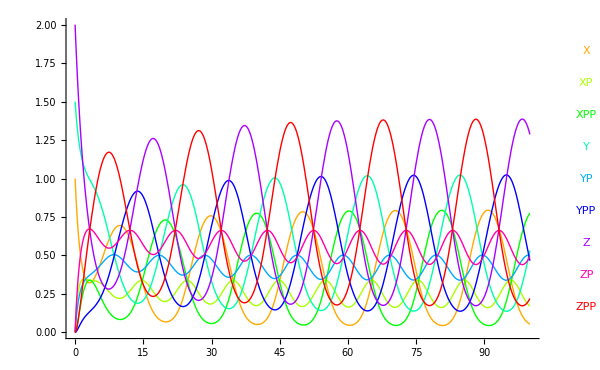

```mathematica
reactions={{Underoverscript[X⟺XP, ZPP, Z],MM[K,v,K,v]},{Underoverscript[XP⟺XPP, ZPP, Z],MM[K,v,K,v]}, {Underoverscript[Y⟺YP, XPP, X],MM[K,v,K,v]},{Underoverscript[YP⟺YPP, XPP, X],MM[K,v,K,v]},
{Underoverscript[Z⟺ZP, YPP, Y],MM[K,v,K,v]},{Underoverscript[ZP⟺ZPP, YPP, Y],MM[K,v,K,v]}};odes=interpret[reactions];
r=run[odes, initialConditions-> {X-> 1, Y-> 1.5, Z-> 2}, rates-> {v-> 1, K-> 2}];
runPlot[r,PlotRange-> All, ImageSize-> 600]
```

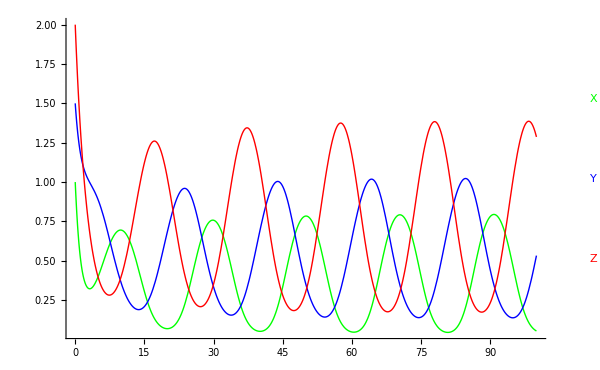

```mathematica
runPlot[r,{X,Y,Z},PlotRange-> All, ImageSize-> 600]
```

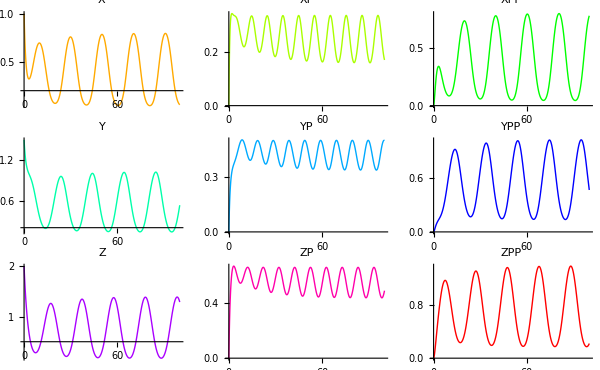

```mathematica
g=gridPlot[r, All, {0,100}, plotColumns-> 3, ImageSize-> 600]
```